# Task 2 N3AS

# Function definitions

```mathematica
(*Define the dispersion relation*)
ωk[k_,m_]:=Sqrt[k^2+m^2];

(*Define the integrand as a function of ε*)
integrand[Ef_,Ei_,q0_,k_,m_,ε_]:=(k^2/(2 Pi)^3)*(1/(ωk[k,m]-I ε))*(1/((q0^2-2 q0 ωk[k,m]+I ε)*((Ei-Ef)^2-2 (Ei-Ef) ωk[k,m]+I ε)*(Ef^2+2 Ef ωk[k,m]+I ε))+1/((q0^2+2 q0 ωk[k,m]+I ε)*((Ei+q0-Ef)^2-2 (Ei+q0-Ef) ωk[k,m]+I ε)*((q0+Ef)^2+2 (q0+Ef) ωk[k,m]+I ε))+1/(((Ef-Ei)^2-2 (Ef-Ei) ωk[k,m]+I ε)*((q0+Ef-Ei)^2-2 (q0+Ef-Ei) ωk[k,m]+I ε)*(Ei^2+2 Ei ωk[k,m]+I ε))+1/((Ef^2-2 Ef ωk[k,m]+I ε)*((q0+Ef)^2-2 (q0+Ef) ωk[k,m]+I ε)*(Ei^2-2 Ei ωk[k,m]+I ε)));

(*Define the integral as a function of ε*)
Int[Ef_,Ei_,q0_,m_,ε_]:=Quiet[NIntegrate[integrand[Ef,Ei,q0,k,m,ε],{k,0,∞}]];

(*Fix m=1*)
m=1;
```

# Plots

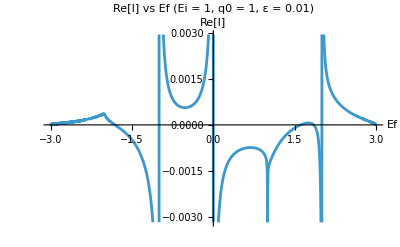

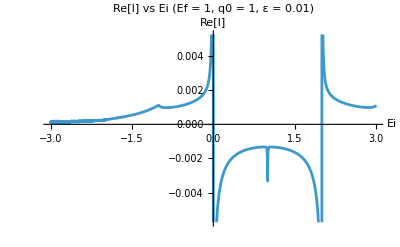

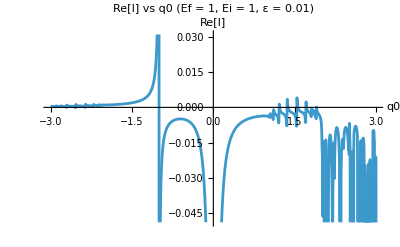

```mathematica
(*Plot Real[I] vs Ef for fixed Ei and q0*)
Plot[Re[Int[Ef,1,1,m,0.01]],{Ef,-3,3},PlotLabel->"Re[I] vs Ef (Ei = 1, q0 = 1, ε = 0.01)",AxesLabel->{"Ef","Re[I]"}]

(*Plot Real[I] vs Ei for fixed Ef and q0*)
Plot[Re[Int[1,Ei,1,m,0.01]],{Ei,-3,3},PlotLabel->"Re[I] vs Ei (Ef = 1, q0 = 1, ε = 0.01)",AxesLabel->{"Ei","Re[I]"}]

(*Plot Real[I] vs q0 for fixed Ef and Ei*)
Plot[Re[Int[1,1,q0,m,0.01]],{q0,-3,3},PlotLabel->"Re[I] vs q0 (Ef = 1, Ei = 1, ε = 0.01)",AxesLabel->{"q0","Re[I]"}]
```